```mathematica
<<MaTeX`
mixe=Import[NotebookDirectory[]<>"mixe.dat"];
mixmu=Import[NotebookDirectory[]<>"mixmu.dat"];
mixtau=Import[NotebookDirectory[]<>"mixtau.dat"];
```

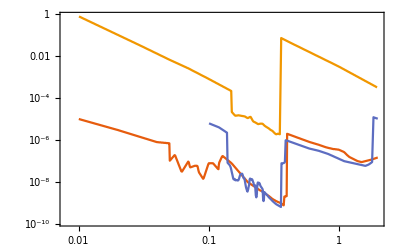

```mathematica
ListLogLogPlot[{mixe,mixmu,mixtau},Joined->True,PlotTheme->"Scientific"]
```

```mathematica
i=1;
While[i<=Dimensions[mixe][[1]],
If[mixe[[i,1]]<0.1,mixe=Delete[mixe,i];,i=i+1;];
]
i=1;
While[i<=Dimensions[mixmu][[1]],
If[mixmu[[i,1]]<0.1,mixmu=Delete[mixmu,i];,i=i+1;];
]
i=1;
While[i<=Dimensions[mixtau][[1]],
If[mixtau[[i,1]]<0.1,mixtau=Delete[mixtau,i];,i=i+1;];
]
```

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
magnificationtext=0.9;
latexe=MaTeX["e",Magnification->magnificationaxes,ContentPadding->False];
latexmu=MaTeX["\\mu",Magnification->magnificationaxes,ContentPadding->False];
latextau=MaTeX["\\tau",Magnification->magnificationaxes,ContentPadding->False];
xlabel=MaTeX["m_\\text{HNL} \\text{(GeV)}",Magnification->magnificationaxes,ContentPadding->False];
ylabelcm2=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\left|U_\\alpha\\right|^2",Magnification->magnificationaxes,ContentPadding->False];
ylabelbarcm2=MaTeX["\\bar{\\nu}/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];ylabelbar=MaTeX["\\bar{\\nu}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
```

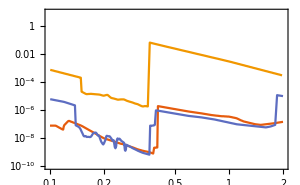

/home/sane/mainhnlchain/mainconfig/mixings.pdf

```mathematica
plotrange={{0.1,2},{10^-10,10}};
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
imagesize={300,Automatic};
legends={latexe,latexmu,latextau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01],{0.9,0.82}];
plotexp=ListLogLogPlot[{mixe,mixmu,mixtau},Joined->True,PlotTheme->"Scientific",PlotRange->plotrange,FrameLabel->framelabel,ImageSize->imagesize,PlotLegends->plotlegends]
Export[NotebookDirectory[]<>"mixings.pdf",plotexp]
```